# Structural estimation

This file estimates ρ and ℶ for college graduates by matching simulated and empirical medians of the wealth to income ratio across 7 age groups.

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
SeedRandom[100];
Off[General::"spell1"]; 
Off[InterpolatingFunction::"dmval"];
```

```mathematica
ClearAll[PrintMemoryInUse];
PrintMemoryInUse:= Block[{},
Print["Current Memory in Use is: ", N[MemoryInUse[]/1024/1024]," Mb."];
];
PrintMemoryInUse;
```

Current Memory in Use is: 86.2753 Mb.

## Setup

```mathematica
<<setup_ConsFn.m;               (* Load parameters and routines to solve for the age-varying consumption functions *)
```

```mathematica
<<setup_Sim.m;                      (* Load parameters and routines to compute simulated medians *)
```

```mathematica
<<setup_Estimation.m;      (* Load "GapEmpiricalSimulatedMedians" function *)
```

```mathematica
<< setup_GPUfuncs.m;      (* load in OpenCL functions *)
```

<program source>:173:28: warning: double precision constant requires cl_khr_fp64, casting to single precision
                Cons = m - 0.000001;
                           ^

<program source>:83:30: warning: double precision constant requires cl_khr_fp64, casting to single precision
        NextWealth = Assets*(1.03/(Gamma[t]*Psi));
                             ^

```mathematica
<<SCFdata.m ;                          (* Load SCF data *)
```

```mathematica
PrintMemoryInUse;
```

Current Memory in Use is: 87.5904 Mb.

## Estimation

```mathematica
VerboseOutput=True;
T0=SessionTime[];
ConstructSimShocks;                    (* Constructs shocks for each agent at each time, function defined in setup_Sim.m  *)
T1=SessionTime[];
If[VerboseOutput==True, Print["Time used (min): ", (T1 - T0)/60];];
(* Around 0.12 minutes for simulating 10000 people under the new analytical method. *)
```

Time used (min): 0.0192644

```mathematica
VerboseOutput=True;
CPUVsGPUTestOption==True;
{ρMin,ρGuess,ρMax,ℶMin,ℶGuess,ℶMax}   = {2,4,8,0.85,0.98,1.05};    
(* Boundaries of the search region *)
UseGPU = False;
X = GapEmpiricalSimulatedMedians[ρGuess,ℶGuess]
```

Step1 Time used (min): 0.010269

Step2 Time used (min): 0.0043596

Step3 Time used (min): 0.004422

46072.9

```mathematica
UseGPU = True;
Y = GapEmpiricalSimulatedMedians[ρGuess,ℶGuess]
X-Y
```

Step1 Time used (min): 0.0006616

Step2 Time used (min): 0.010984

Step3 Time used (min): 0.0023781

45321.6

0.00131288

```mathematica
PrintMemoryInUse;
```

Current Memory in Use is: 667.885 Mb.

Current Memory in Use is: 55.2515 Mb.

### Using CPU vs GPU:

```mathematica
ClearAll[CPUVsGPUFunc];
CPUVsGPUFunc[ρ_,ℶ_] := Block[{UseGPU, GapCPU, GapGPU , TimeMatrix, GapMatrix, TimeCPU, TimeGPU
, TEnd1, TStart1
, TEnd2, TStart2
, TEnd3, TStart3},

CPUVsGPUTestOption=True;
VerboseOutput=False;


UseGPU = False;
T0=SessionTime[];
GapCPU=GapEmpiricalSimulatedMedians[ρ,ℶ];
T1=SessionTime[];
If[VerboseOutput==True, Print["Total Time used (min): ", (T1 - T0)/60]
; Print["GapEmpiricalSimulatedMedians[ρ,ℶ]=", GapCPU, " under CPU"];
];
TimeCPU={(TEnd1 - TStart1)
, (TEnd2 - TStart2)
, (TEnd3 - TStart3)
,  (T1 - T0)}/60;

 UseGPU = OpenCLQ[];
 If[UseGPU==False
, Print["Error: No GPU supported on this computer!"];
Quit[];
];
T0=SessionTime[];
GapGPU=GapEmpiricalSimulatedMedians[ρ,ℶ];
T1=SessionTime[];
If[VerboseOutput==True, Print["Total Time used (min): ", (T1 - T0)/60];
;Print["GapEmpiricalSimulatedMedians[ρ,ℶ]=", GapGPU, " under GPU"];
];
TimeGPU={(TEnd1 - TStart1)
, (TEnd2 - TStart2)
, (TEnd3 - TStart3)
,  (T1 - T0)}/60;


TimeMatrix={{ TimeCPU[[1]], TimeGPU[[1]],TimeCPU[[1]]/ TimeGPU[[1]]}
, { TimeCPU[[2]], TimeGPU[[2]],TimeCPU[[2]]/ TimeGPU[[2]]}
, { TimeCPU[[3]], TimeGPU[[3]],TimeCPU[[3]]/ TimeGPU[[3]]}
, { TimeCPU[[4]], TimeGPU[[4]],TimeCPU[[4]]/ TimeGPU[[4]]}
};
GapMatrix={{GapCPU, GapGPU,(GapGPU-GapCPU)/GapCPU
}};
Print["Running Time Comparison under {ρ, ℶ}= {", ρ, ",", ℶ, "}:"];
Print[TableForm[TimeMatrix,TableHeadings->{{"SolveConFunc","SimulateEcon","ComputeTheGap", "TotTimeUsed"},{"TimeCPU", "TimeGPU", "TimeCPU/TimeGPU"}}
,TableAlignments->Center,TableSpacing->{1.8,5}]];
Print["Computed Gap Comparison under {ρ, ℶ}= {", ρ, ",",  ℶ, "}:"];
Print[TableForm[GapMatrix,TableHeadings->{{},{"GapCPU", "GapGPU", "(GapGPU-GapCPU)/GapCPU"}}
,TableAlignments->Center,TableSpacing->{1.8,5}]];
PrintMemoryInUse;
];
```

```mathematica
{ρThis,ℶThis}={ρGuess,ℶGuess};
CPUVsGPUFunc[ρThis,ℶThis];
```

Running Time Comparison under {ρ, ℶ}= {4,0.98}:

| TimeCPU | TimeGPU | TimeCPU/TimeGPU
SolveConFunc | 0.01378018 | 0.01378018 | 1.
SimulateEcon | 0.30576392 | 0.00520007 | 58.8
ComputeTheGap | 0.00208003 | 0.00208003 | 1.
TotTimeUsed | 0.32162412 | 0.02106027 | 15.2716

Computed Gap Comparison under {ρ, ℶ}= {4,0.98}:

| GapCPU | GapGPU | (GapGPU-GapCPU)/GapCPU
 | 45486. | 45485.9 | -3.61335×10^-8

Current Memory in Use is: 105.873 Mb.

```mathematica
{Max[Abs[mtSimMatCPU[[-1]]-mtSimMatGPU[[-1]]]]
, Max[Abs[ctSimMatCPU[[-1]]-ctSimMatGPU[[-1]]]]
, Max[Abs[atSimMatCPU[[-1]]-atSimMatGPU[[-1]]]]
, Max[Abs[wtSimMatCPU[[-1]]-wtSimMatGPU[[-1]]]]}
```

{6.25101×10^-6,3.86037×10^-7,5.95509×10^-6,6.26886×10^-6}

```mathematica
ClearAll[mtSimMatCPU, ctSimMatCPU, atSimMatCPU, wtSimMatCPU];
ClearAll[mtSimMatGPU, ctSimMatGPU, atSimMatGPU, wtSimMatGPU];
PrintMemoryInUse;
```

Current Memory in Use is: 88.1656 Mb.

```mathematica
{ρThis,ℶThis}={ρMin,ℶMin};
CPUVsGPUFunc[ρThis,ℶThis];
ClearAll[mtSimMatCPU, ctSimMatCPU, atSimMatCPU, wtSimMatCPU];
ClearAll[mtSimMatGPU, ctSimMatGPU, atSimMatGPU, wtSimMatGPU];
PrintMemoryInUse;
```

Running Time Comparison under {ρ, ℶ}= {2,0.85}:

| TimeCPU | TimeGPU | TimeCPU/TimeGPU
SolveConFunc | 0.01456019 | 0.01456019 | 1.
SimulateEcon | 0.33306427 | 0.00494006 | 67.4211
ComputeTheGap | 0.00208003 | 0.00208003 | 1.
TotTimeUsed | 0.34970448 | 0.02158028 | 16.20482

Computed Gap Comparison under {ρ, ℶ}= {2,0.85}:

| GapCPU | GapGPU | (GapGPU-GapCPU)/GapCPU
 | 54338.5 | 54338.5 | -5.39094×10^-9

Current Memory in Use is: 125.039 Mb.

```mathematica
{ρThis,ℶThis}={ρMin,ℶMax};
CPUVsGPUFunc[ρThis,ℶThis];
ClearAll[mtSimMatCPU, ctSimMatCPU, atSimMatCPU, wtSimMatCPU];
ClearAll[mtSimMatGPU, ctSimMatGPU, atSimMatGPU, wtSimMatGPU];
PrintMemoryInUse;
```

Running Time Comparison under {ρ, ℶ}= {2,1.05}:

| TimeCPU | TimeGPU | TimeCPU/TimeGPU
SolveConFunc | 0.01456019 | 0.01456019 | 1.
SimulateEcon | 0.34450442 | 0.00494006 | 69.7368
ComputeTheGap | 0.00208003 | 0.00234003 | 0.88889
TotTimeUsed | 0.36114463 | 0.02184028 | 16.53571

Computed Gap Comparison under {ρ, ℶ}= {2,1.05}:

| GapCPU | GapGPU | (GapGPU-GapCPU)/GapCPU
 | 63090.9 | 63090.9 | 2.10668×10^-7

Current Memory in Use is: 135.687 Mb.

```mathematica
{ρThis,ℶThis}={ρMax,ℶMin};
CPUVsGPUFunc[ρThis,ℶThis];
ClearAll[mtSimMatCPU, ctSimMatCPU, atSimMatCPU, wtSimMatCPU];
ClearAll[mtSimMatGPU, ctSimMatGPU, atSimMatGPU, wtSimMatGPU];
PrintMemoryInUse;
```

Running Time Comparison under {ρ, ℶ}= {8,0.85}:

| TimeCPU | TimeGPU | TimeCPU/TimeGPU
SolveConFunc | 0.01430018 | 0.01430018 | 1.
SimulateEcon | 0.31876409 | 0.00520007 | 61.3
ComputeTheGap | 0.00208003 | 0.00208003 | 1.
TotTimeUsed | 0.3351443 | 0.02158028 | 15.53012

Computed Gap Comparison under {ρ, ℶ}= {8,0.85}:

| GapCPU | GapGPU | (GapGPU-GapCPU)/GapCPU
 | 46114.1 | 46114.1 | 1.13108×10^-9

Current Memory in Use is: 146.435 Mb.

Current Memory in Use is: 119.711 Mb.

```mathematica
{ρThis,ℶThis}={ρMax,ℶMax};
CPUVsGPUFunc[ρThis,ℶThis];
ClearAll[mtSimMatCPU, ctSimMatCPU, atSimMatCPU, wtSimMatCPU];
ClearAll[mtSimMatGPU, ctSimMatGPU, atSimMatGPU, wtSimMatGPU];
PrintMemoryInUse;
```

Running Time Comparison under {ρ, ℶ}= {8,1.05}:

| TimeCPU | TimeGPU | TimeCPU/TimeGPU
SolveConFunc | 0.01404018 | 0.01430018 | 0.981818
SimulateEcon | 0.32292414 | 0.00494006 | 65.3684
ComputeTheGap | 0.00234003 | 0.00208003 | 1.125
TotTimeUsed | 0.33930435 | 0.02132027 | 15.91463

Computed Gap Comparison under {ρ, ℶ}= {8,1.05}:

| GapCPU | GapGPU | (GapGPU-GapCPU)/GapCPU
 | 47572. | 47572. | 8.03876×10^-8

Current Memory in Use is: 157.122 Mb.

Current Memory in Use is: 130.398 Mb.

### Estimate Under CPU:

```mathematica
VerboseOutput=False;
UseGPU = False;
CPUVsGPUTestOption=False;
PrintMemoryInUse;
```

Current Memory in Use is: 107.301 Mb.

```mathematica
(* Solving for ρ and ℶ which minimize the "GapEmpiricalSimulatedMedians" function *)
TimeFMin = SessionTime[];
{min,{steps}} =Reap[FindMinimum[GapEmpiricalSimulatedMedians[ρ,ℶ],{ρ,ρGuess,ρMin,ρMax},{ℶ,ℶGuess,ℶMin,ℶMax},WorkingPrecision->40, StepMonitor :> Sow[{ρ,ℶ}]]] 
Print["Time for FindMinimum (min): ", NumberForm[(SessionTime[] - TimeFMin)/60,3]];
(* Old method needs 0.06 minutes for each trial. New method needs 0.40 minutes for each trial. 
Total minutes needed: 50*20 minutes expected.
That is too long. Hence I comment this part out. 
*)
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 20. digits of working precision to meet these tolerances.

{{41813.82735128862987,{ρ→5.293512055825838292,ℶ→1.0014355917967378604}},{{{4.00047,1.01146},{4.00048,1.01167},{4.00048,1.0117},{4.00048,1.0117},{4.00048,1.0117},{4.02385,1.01131},{4.02117,1.01136},{4.02243,1.01134},{4.02226,1.01135},{4.17051,1.01107},{4.26456,1.01086},{4.24322,1.01087},{4.24234,1.01077},{4.6066,1.00832},{4.897,1.00625},{4.91948,1.00598},{4.8959,1.00534},{4.91387,1.00506},{5.11569,1.00311},{5.28996,1.00143},{5.31047,1.00124},{5.2983,1.00138},{5.29371,1.00143},{5.29442,1.00142},{5.29437,1.00142},{5.29412,1.00142},{5.2935122508466249632,1.001435577907193453},{5.2935121388797609703,1.0014355856827152496},{5.293512055208896651,1.0014355917957584816},{5.2935120552608079184,1.0014355917929232295},{5.2935120552925567002,1.0014355917981968821},{5.2935120558256805408,1.0014355917967454353}}}}

Time for FindMinimum (min): 3.31

```mathematica
ρEstimate =ρ/.min[[2, 1]];
ℶEstimate =ℶ/.min[[2, 2]];
```

5.293512055825838292

1.0014355917967378604

### Estimate Under GPU:

```mathematica
VerboseOutput=False;
UseGPU = OpenCLQ[];
PrintMemoryInUse;
```

Current Memory in Use is: 55.2547 Mb.

```mathematica
(* Solving for ρ and ℶ which minimize the "GapEmpiricalSimulatedMedians" function *)
TimeFMin = SessionTime[];
{min,{steps}} =Reap[FindMinimum[GapEmpiricalSimulatedMedians[ρ,ℶ],{ρ,ρGuess,ρMin,ρMax},{ℶ,ℶGuess,ℶMin,ℶMax},WorkingPrecision->40, StepMonitor :> Sow[{ρ,ℶ}]]] 
Print["Time for FindMinimum (min): ", NumberForm[(SessionTime[] - TimeFMin)/60,3]];
PrintMemoryInUse;
(* Old method needs 0.06 minutes for each trial. New method needs 0.02 minutes for each trial. 
Total minutes needed: 50 minutes or less. *)
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{41739.58696526100538903847336769104003906,{ρ→4.001192563810264779533554246881976723671,ℶ→1.014085143580117254202832555165514349937}},{{{4.00079,1.01075},{4.00111,1.01381},{4.00113,1.01412},{4.00117,1.0141},{4.0012,1.01408},{4.0012,1.01408}}}}

Time for FindMinimum (min): 1.90

Current Memory in Use is: 1007.32 Mb.

```mathematica
(* JYao: The objective function is discontinuous, using the default method requires finding the derivative. The following line avoids this by using the PrincipalAxis method, which gives a different result. The drawback is that it takes a longer time. *)
(*TimeFMin = SessionTime[];
{min,{steps}} =Reap[FindMinimum[GapEmpiricalSimulatedMedians[ρ,ℶ],{ρ,ρGuess,ρMin,ρMax},{ℶ,ℶGuess,ℶMin,ℶMax},WorkingPrecision->20,Method->"PrincipalAxis",StepMonitor :> Sow[{ρ,ℶ}]]] 
Print["Time for FindMinimum (min): ", NumberForm[(SessionTime[] - TimeFMin)/60,3]];
PrintMemoryInUse;*)
```

{{41781.427145426096104,{ρ→6.4198781541997817458,ℶ→0.99119828497516832038}},{{{6.91754,0.980901},{6.5955,0.988794},{6.41988,0.991198},{6.41988,0.991198},{6.4198781540769271377,0.99119828504402924146},{6.4198781541997817458,0.99119828497516832038}}}}

Time for FindMinimum (min): 8.58

Current Memory in Use is: 5182.07 Mb.

```mathematica
(* Solving for ρ and ℶ which minimize the "GapEmpiricalSimulatedMedians" function *)
TimeFMin = SessionTime[];
RecordProgress = True;
TriedTheseGuesses = {};
If [UseGPU,
{ρLB,ρUB,ℶLB,ℶUB} = MNWgridSearch[ρMin,ρMax,ℶMin,ℶMax,15];
{ρLB2,ρUB2,ℶLB2,ℶUB2} = MNWgridSearch[ρLB,ρUB,ℶLB,ℶUB,15];
ρGuess = (ρLB2+ρUB2)/2;
ℶGuess = (ℶLB2+ℶUB2)/2;
ρMin = ρGuess-0.2;
ρMax = ρGuess+0.2;
ℶMin = ℶGuess-0.01;
ℶMax = ℶGuess+0.01;
(*
UseGPU = False;
*)
];
{min,{steps}} =Reap[FindMinimum[GapEmpiricalSimulatedMedians[ρ,ℶ],{ρ,ρGuess,ρMin,ρMax},{ℶ,ℶGuess,ℶMin,ℶMax}, StepMonitor :> Sow[{ρ,ℶ}]]];
Print["Time for FindMinimum (minutes): ", NumberForm[(SessionTime[] - TimeFMin)/60,3]];
PrintMemoryInUse;
(* Old method needs 0.06 minutes for each trial. New method needs 0.02 minutes for each trial. 
Total minutes needed: 20 minutes. *)
```

$Aborted

$Aborted

Time for FindMinimum (minutes): 0.327

Current Memory in Use is: 54.3226 Mb.

```mathematica
ρEstimate =ρ/.min[[2, 1]];
ℶEstimate =ℶ/.min[[2, 2]];
```

### Second Round Estimation

```mathematica
CPUVsGPUTestOption=True;
Construct𝒸FuncLife[ρEstimate,ℶEstimate];
If[UseGPU,SimulateGPU;
WeightAgeGroup =Table[PDF[SmoothKernelDistribution[Table[Median[wtSimMatGPU[[s]]],{s,1,SimPeriods}]],
SimMedian[[t]]],{t,1,Length[SimMedian]}];
,Simulate;
WeightAgeGroup =Table[PDF[SmoothKernelDistribution[Table[Median[wtSimMatCPU[[s]]],{s,1,SimPeriods}]],
SimMedian[[t]]],{t,1,Length[SimMedian]}]
]; 
CPUVsGPUTestOption=False;
(* JYao: this line computes the empirical density of 
the distribution of wealth of agents of age t at the median. It is a
nonparametric estimate with Gaussian kernel*)
```

```mathematica
TimeFMin = SessionTime[];{min2,{steps2}} =Reap[FindMinimum[GapEmpiricalSimulatedMediansSecondRound[ρ,ℶ],{ρ,ρGuess,ρMin,ρMax},{ℶ,ℶGuess,ℶMin,ℶMax},WorkingPrecision->40, (*Method->"PrincipalAxis",*)StepMonitor :> Sow[{ρ,ℶ}]]];
Print["Time for FindMinimum (minutes): ", NumberForm[(SessionTime[] - TimeFMin)/60,3]];
PrintMemoryInUse;
ρEstimateSecondRound =ρ/.min2[[2, 1]];
ℶEstimateSecondRound =ℶ/.min2[[2, 2]];
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Time for FindMinimum (minutes): 2.14

Current Memory in Use is: 2029.63 Mb.

```mathematica
ρEstimateSecondRound
```

4.001182798126234452240623795660212635994

```mathematica
ℶEstimateSecondRound
```

1.013608779702698248215142484696116298437

```mathematica
WeightAgeGroup
```

{0.128013,0.198601,0.243027,0.25623,0.237744,0.197727,0.147436}

### Contour Plot:

```mathematica
UseGPU = OpenCLQ[];
{ρMin,ρMax,ℶMin,ℶMax}   = {2,8,0.85,1.05};
```

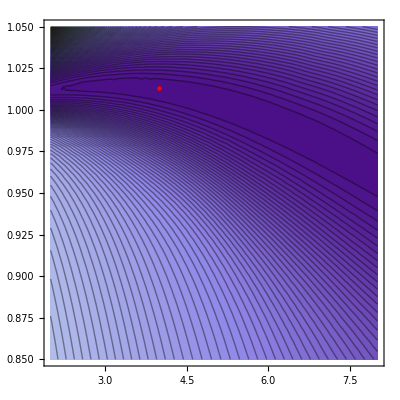

Time for contour plot (min):  80.7

Current Memory in Use is:  41.5866  Mb.

```mathematica
(* Contour plot of the "GapEmpiricalSimulatedMedian" function. With MaxRecursion->1 40 minutes are needed to obtain the contourplot*)
TimeContourPlot = SessionTime[];
ContourPlotMedianStrEst=ContourPlot[GapEmpiricalSimulatedMedians[ρ,ℶ],{ρ,ρMin,ρMax},{ℶ,ℶMin,ℶMax},Mesh->None, MaxRecursion->2,PlotPoints->10,Contours->100];
PlotContourMedianStrEst=Show[{ContourPlotMedianStrEst,
ListPlot[{{ρEstimate,ℶEstimate}},PlotStyle->Directive[PointSize[Large],Red]]}]
Print["Time for contour plot (min): ", NumberForm[(SessionTime[] - TimeContourPlot)/60,3]] ;
(* Total minutes needed: 90 minutes. *)
PrintMemoryInUse;
```

```mathematica
Export["../../../Figures/PlotContourMedianStrEst.pdf",PlotContourMedianStrEst];
Export["../../../Figures/PlotContourMedianStrEst.eps",PlotContourMedianStrEst];
```

```mathematica
ClearAll[ContourPlotMedianStrEst];
ClearAll[PlotContourMedianStrEst];
PrintMemoryInUse;
```

## Bootstrap

```mathematica
{ρMin,ρMax,ℶMin,ℶMax}   = {2,8,0.85,1.05};
```

```mathematica
<<setup_Bootstrap.m   (* Loading bootstrap parameters and "Bootstrap" routine *)
(* In the nootstrap.m, we use the method of "principal axis" in the FindMin. This turns out to be better than the "Automatic" method. *)
```

```mathematica
PrintMemoryInUse;
```

Current Memory in Use is: 1816.61 Mb.

```mathematica
TimeBootstrap=SessionTime[];
Bootstrap (* Computing standard errors *)
```

Number of bootstrap: 1

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 20. digits of working precision to meet these tolerances.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 6.66

Current Memory in Use is: 3141.34 Mb.

Number of bootstrap: 2

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 12.1

Current Memory in Use is: 3867.72 Mb.

Number of bootstrap: 3

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 16.1

Current Memory in Use is: 3910.45 Mb.

Number of bootstrap: 4

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 21.7

Current Memory in Use is: 4722.29 Mb.

Number of bootstrap: 5

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 25.6

Current Memory in Use is: 4765.02 Mb.

Number of bootstrap: 6

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 20. digits of working precision to meet these tolerances.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 31.8

Current Memory in Use is: 5790.52 Mb.

Number of bootstrap: 7

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum :: fmgz will be suppressed during this calculation.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 35.7

Current Memory in Use is: 5833.26 Mb.

Number of bootstrap: 8

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 40.6

Current Memory in Use is: 6303.28 Mb.

Number of bootstrap: 9

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 44.9

Current Memory in Use is: 6474.2 Mb.

Number of bootstrap: 10

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 49.6

Current Memory in Use is: 6901.48 Mb.

Number of bootstrap: 11

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 53.6

Current Memory in Use is: 6944.22 Mb.

Number of bootstrap: 12

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 57.5

Current Memory in Use is: 6986.95 Mb.

Number of bootstrap: 13

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 61.4

Current Memory in Use is: 7029.69 Mb.

Number of bootstrap: 14

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 65.4

Current Memory in Use is: 7072.42 Mb.

Number of bootstrap: 15

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 69.3

Current Memory in Use is: 7115.16 Mb.

Number of bootstrap: 16

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 73.3

Current Memory in Use is: 7157.9 Mb.

Number of bootstrap: 17

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 77.2

Current Memory in Use is: 7200.63 Mb.

Number of bootstrap: 18

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 83.8

Current Memory in Use is: 8439.74 Mb.

Number of bootstrap: 19

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 87.8

Current Memory in Use is: 8482.48 Mb.

Number of bootstrap: 20

ρ,ℶ: {4.00,1.01}

Cumulative boostrap time (min): 91.8

Current Memory in Use is: 8525.21 Mb.

Estimated params: (3.9978731284478468133 | 1.0132787939904301935
3.9978731284478468133 | 1.0132787945416103209
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787922445005722
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301928
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787867343171472
3.9978731284478468133 | 1.0125070367930181497
3.9978731284478468133 | 1.0111177249065357578
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132788001305455302
3.9978731284478468133 | 1.0132787939904301933
3.9978731284478468133 | 1.0132787939904301933)

Standard errors for {ρ,ℶ}: {0.,0.000504493}

```mathematica
ParamsBootstrap
```

{{ρ/.minFMin⟦2,1⟧,ℶ/.minFMin⟦2,2⟧},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
{ρMin,ρGuess,ρMax,ℶMin,ℶGuess,ℶMax}   = {2,4,8,0.85,0.98,1.05};
```